```mathematica
(*Method:Do Loop*)
(*The reason we don't use recursive definition is because it is limited by the recursion depth,if we choose a relatively large number as our input*)
(*pArray is the array of product result*)
a[n_]:=(n^2+1)/(n^2-1) ;
t[n_]:=If[PrimeQ[n],a[n],1];
```

```mathematica
Clear[pArray]
```

```mathematica
pArray[n_]:=Module[{ },
array=Table[1,n];(*Using Table here is better than array*)
(*If we want to use array to generate duplicate numbers ,then we first need to define a function*)
Do[array=ReplacePart[array,k->array[[k-1]]*t[k]],{k,2,n}];
(*Replace the kth element in the array*)
array=ReplacePart[array,1->a[2]];
N[array](*Numerical Output*)
];
p[n_]:=pArray[n][[n]];
```

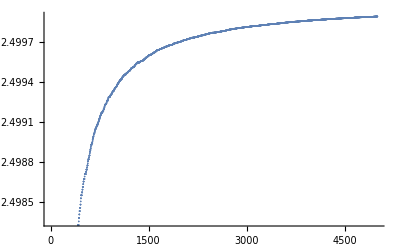

```mathematica
(*Draw a graph of the calculation result,so that we can roughly judge whether the result converges*)
ListPlot[pArray[5000]]
(*If we use Do Loop to creat such an array ,then the efficiency will be relatively high when drawing.Since we can get the value of p[n+1] from p[n] without having to calculate them separately*)
```